```mathematica
Costo[t_]:=9.99-0.79Floor[-(t-1)]
```

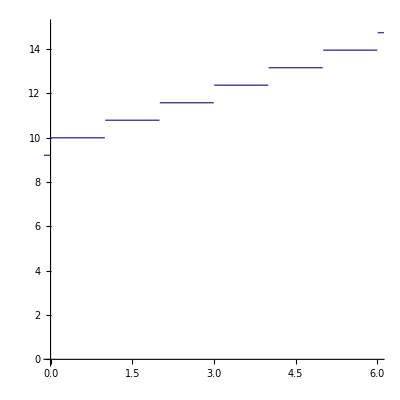

```mathematica
Plot[Costo[t],{t,-10,10},PlotRange->{{0,6},{0,15}}, AspectRatio->1]
```

```mathematica
Grid[Table[{t,N[Costo[t],5]},{t,3,4.1,0.1}], Frame->All]
```

3. | 11.57
3.1 | 12.36
3.2 | 12.36
3.3 | 12.36
3.4 | 12.36
3.5 | 12.36
3.6 | 12.36
3.7 | 12.36
3.8 | 12.36
3.9 | 12.36
4. | 12.36
4.1 | 13.15

```mathematica
Limit[Costo[t],t->3.5]
```

12.36

```mathematica
Limit[Costo[t],t->3,Direction->1]
```

11.57

```mathematica
Limit[Costo[t],t->3,Direction->-1]
```

12.36

```mathematica
(*El límite no existe en t=3 porque tiende a 11.57 por la izquierda y a 12.36 por la derecha*)
```

```mathematica
f1[x_]:=Expand[(Sqrt[x+5]-3)/(x-4)]   (*El dominio es [-5, +INF)-{4} *)
```

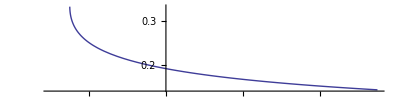

```mathematica
Plot[f1[x],{x,-6,11}, AspectRatio->1/4]
```

```mathematica
(*Por la forma de la gráfica se puede pensar que la función es lineal de -5 al infinito positivo, pero no es así porque la función no está definida en el punto x=4, el hueco en ese punto no se ve. Por eso es importante analizar de forma analítica la función y no guiarse sólo por la gráfica, la gráfica es sólo una referencia pero no muestra las discontinuidades*)


f2[x_]:=Expand[2x+1]

Manipulate[{Plot[f2[x],{x,1-a,1+a},PlotRange->{{-2,5},{-2,6}}],Abs[f2[a+1]-3],N[Abs[f2[1-a]-3]]},{a,0.0001,1,0.0001}]
```

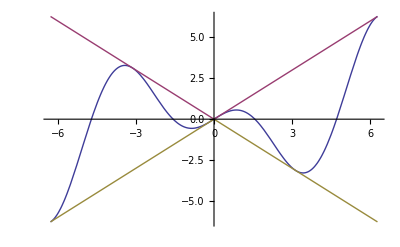

Plot::nonopt: Options expected (instead of {x, -0.1, 0.1}) beyond position 3 in Plot[f3[x], f4[x], {x, -0.1, 0.1}]. An option must be a rule or a list of rules.

```mathematica
f3[x_]:=Expand[x Cos[x]];
f4[x_]:=Expand[(Abs[x])(Sin[x])];
f5[x_]:=Abs[x Sin[x]]
f6[x_]:=x Sin [1/x]
f7[x_]:=Abs[x]Cos[x]
f8[x_]:=x Cos [1/x]

Plot[{f3[x],Abs[x],-Abs[x]},{x,-2 Pi,2 Pi}]
```